# Notebook 02: Relative Coordinates

## William J Turkel, wturkel@uwo.ca Digital Humanities 1011B

## Absolute coordinates

Last class we learned how to build up a graphic image, and to give a collection of commands a name.

```mathematica
ufo={Orange,Disk[{0,0},{3,1}],LightOrange,Disk[{0,1/2},{3/2,1}]};
```

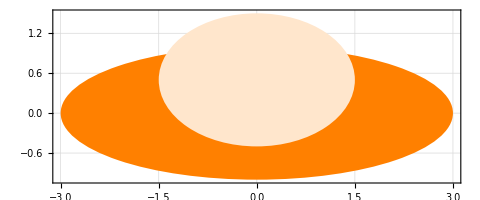

```mathematica
Graphics[ufo,GridLines->Automatic,Frame->True]
```

This definition of ufo includes the centres of both the main body (orange disk) {0,0} and the cockpit (light orange disk) {0,1/2}. So the ufo can only be drawn in one place.

### Drawing multiple copies

What if we want to draw two ufos? Since we are using absolute coordinates, we have to create a second symbol where we have adjusted all of the coordinates, so both will fit in the same drawing.

```mathematica
ufo2={Orange,Disk[{8,-1},{3,1}],LightOrange,Disk[{8,-1/2},{3/2,1}]};
```

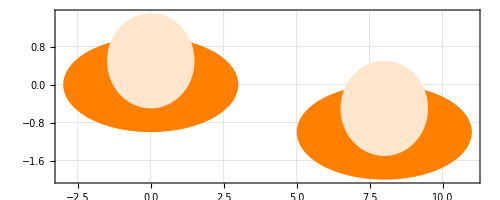

```mathematica
Graphics[Join[ufo,ufo2],GridLines->Automatic,Frame->True]
```

This can be tedious and error prone, especially if we want to draw a lot of objects.  It would be much better if we were able to reuse our ufo drawing. Relative coordinates allow us to do this.

## Relative coordinates

### The semiaxes of an ellipse

Recall that we can plot an ellipse by specifying the centre, and the lengths of its horizontal and vertical semiaxes. In the figure below, the horizontal semiaxis (blue) has a length of 3, and the vertical semiaxis (red) has a length of 2. The ellipse is centred at {0, 0}.

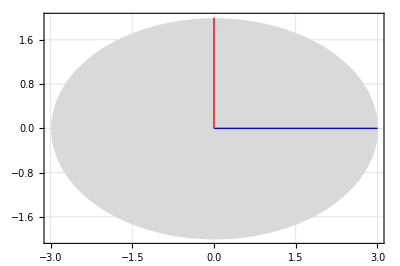

```mathematica
Graphics[{LightGray,Disk[{0,0},{3,2}],Blue,Line[{{0,0},{3,0}}],Red,Line[{{0,0},{0,2}}]},GridLines->Automatic,Frame->True]
```

We will learn how to use Line below.

### Absolute coordinates

Absolute coordinates say exactly where something is. Here are the absolute coordinates for our ufo...

```mathematica
ufo
```

{RGBColor[1, 0.5, 0],Disk[{0,0},{3,1}],RGBColor[1, 0.9, 0.8],Disk[{0,1/2},{3/2,1}]}

The centre of the main body is {0,0}, the length of the horizontal semiaxis is 3 and the length of the vertical semiaxis is 1.

The centre of the cockpit is {0,1/2}, the length of the horizontal semiaxis is 3/2 and the length of the vertical semiaxis is 1.

```mathematica
Graphics[ufo,GridLines->Automatic,Frame->True]
```

-Graphics-

### Relative coordinates

In a relative coordinate system, we pick a single point which we will call the origin and give it coordinates {x, y}. We then describe all the other measurements with respect to this origin point.

Let’s use the centre of the main body of our ufo as the origin point. Then our list of commands to draw a ufo is going to look like this

{Orange, Disk[{x, y}, {?, ?}], LightOrange, Disk[{?, ?}, {?, ?}]}

Now we need to fill in the question marks. Let’s figure out where the centre of the cockpit is relative to the centre of the main body. They both have the same horizontal (x) measurement, so we can write this:

{Orange, Disk[{x, y}, {?, ?}], LightOrange, Disk[{x, ?}, {?, ?}]}

The vertical (y) measurement of the centre of the cockpit is half a unit greater than the same measurement for the centre of the main body. So we can write:

{Orange, Disk[{x, y}, {?, ?}], LightOrange, Disk[{x, y+1/2}, {?, ?}]}

Now that we know the relative centres of our two ellipses, we can figure out their sizes. This turns out to be quite easy, since the size of the object doesn’t change with its position!

{Orange, Disk[{x, y}, {3, 1}], LightOrange, Disk[{x, y+1/2}, {3/2, 1}]}

### A ufo-drawing function

Now that we have the list we need to describe our ufo in relative coordinates, we can create a function to draw ufos.

The function takes two arguments, which specify the centre position of the object we want to draw. The function looks like this

```mathematica
drawUFO[{x_,y_}]:=
{Orange,Disk[{x,y},{3,1}],LightOrange,Disk[{x,y+1/2},{3/2,1}]}
```

Here is how we use it

```mathematica
Graphics[drawUFO[{0,0}],GridLines->Automatic,Frame->True]
```

-Graphics-

### Drawing multiple ufos

Now we can draw as many ufos as we want. We just give each one different (absolute) centre coordinates.

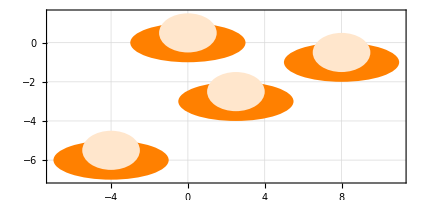

```mathematica
Graphics[{drawUFO[{-4,-6}],drawUFO[{0,0}],drawUFO[{5/2,-3}],drawUFO[{8,-1}]},GridLines->Automatic,Frame->True]
```

## Points and lines

### Point

The Point command draws one or more points at specified coordinates. If you want to draw more than one point, you give the command a list of coordinates.

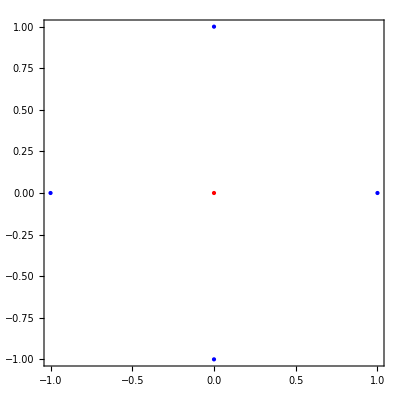

```mathematica
Graphics[{Red,Point[{0,0}],Blue,Point[{{-1,0},{1,0},{0,-1},{0,1}}]},Frame->True]
```

You can increase the size of your points (making them easier to see) with the PointSize command

```mathematica
Graphics[{PointSize[Large],Red,Point[{0,0}],Blue,Point[{{-1,0},{1,0},{0,-1},{0,1}}]},Frame->True]
```

-Graphics-

### Lines and arrows

To plot a line or arrow, you specify a series of points.

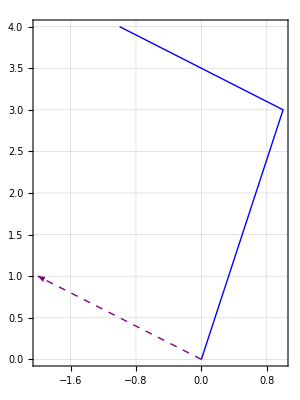

```mathematica
Graphics[{Thick,Blue,Line[{{0,0},{1,3},{-1,4}}],Purple,Dashed,Arrow[{{0,0},{-2,1}}]},GridLines->Automatic,Frame->True]
```

## Tables

The Table command allows us to generate lists of numbers. It is very useful for making a series of regularly spaced coordinates.

Suppose we want a list of five coordinate pairs. The first member of each pair will be 0, the second number will range from 0 to 4. Here is how we use the Table command to generate such a list. The symbol y is a variable which takes on the successive values of 0 through 4.

```mathematica
Table[{0,y},{y,0,4}]
```

{{0,0},{0,1},{0,2},{0,3},{0,4}}

We can use Point to visualize each of these coordinates

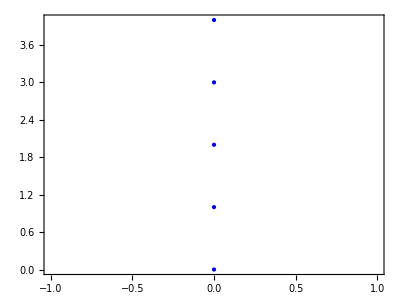

```mathematica
Graphics[{PointSize[Large],Blue,Point[Table[{0,y},{y,0,4}]]},Frame->True]
```

If we want a horizontal row of points we can change the x coordinate instead

```mathematica
Table[{x,0},{x,0,4}]
```

{{0,0},{1,0},{2,0},{3,0},{4,0}}

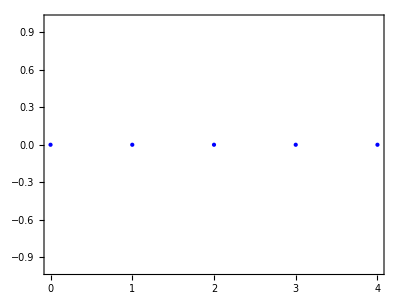

```mathematica
Graphics[{PointSize[Large],Blue,Point[Table[{x,0},{x,0,4}]]},Frame->True]
```

If we use the same value for both x and y coordinates, we get a diagonal line

```mathematica
Table[{i,i},{i,0,4}]
```

{{0,0},{1,1},{2,2},{3,3},{4,4}}

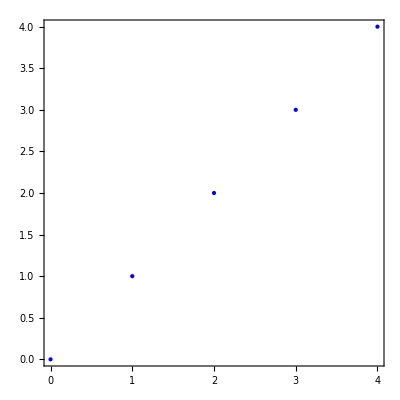

```mathematica
Graphics[{PointSize[Large],Blue,Point[Table[{i,i},{i,0,4}]]},Frame->True]
```

How would you make a diagonal line running in the other direction (from upper left to lower right)?

## A row of trees

Here is a function for drawing a tree

```mathematica
drawTree[{x_,y_}]:=
{Brown,Rectangle[{x-1/16,y},{x+1/16,y-2}],Green,Thick,Line[{{x-2,y},{x+2,y},{x+1,y+1},{x+2,y+1},{x,y+3},{x-2,y+1},{x-1,y+1},{x-2,y}}]}
```

Here is what a single tree looks like

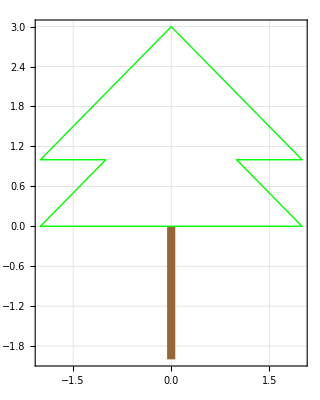

```mathematica
Graphics[drawTree[{0,0}],GridLines->Automatic,Frame->True]
```

Now we can use Table to draw a row of 10 trees like this

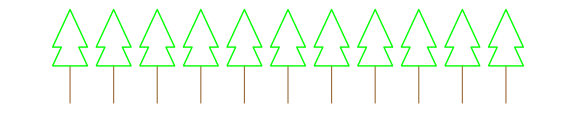

```mathematica
Graphics[Table[drawTree[{x,0}],{x,0,50,5}],ImageSize->Large]
```

Note that we are counting up the x coordinate by 5s to leave some room for each tree

```mathematica
Table[x,{x,0,50,5}]
```

{0,5,10,15,20,25,30,35,40,45,50}

In the next lesson we will see how we would fill in the green part of the tree if we wanted to

## In-Class Activity

### Using relative coordinates, draw a picture that has at least three copies of the same object.

#### NAME:

#### STUDENT NUMBER:

#### DATE:

## Upload your notebook

Don’t forget to upload a copy of your notebook for this day’s class to the OWL Site for the course